```mathematica
Get["/Users/rishi/Developer/localf1/mma/SWModularWorkbench/SWModularWorkbench.wl"];
```

```mathematica
Needs["SWModularWorkbench`"];
```

```mathematica
RichardsonResum[PartSum_,n_]:=With[{d=Length[PartSum]-n-1},Sum[PartSum[[Length[PartSum]+k-n]] (d+k)^n (-1)^(k+n)/k!/(n-k)!,{k,0,n}]];
```

```mathematica
ClearAll[g2g3FromCoeffs,g2g3FromCubic];

(*For y^2=x^3+a2 x^2+a1 x+a0*)
g2g3FromCoeffs[a2_,a1_,a0_]:=Simplify[{g2->4/3 (a2^2-3 a1),g3->4/27 (9 a1 a2-27 a0-2 a2^3)}];

(*For an explicit monic cubic polynomial in x*)
g2g3FromCubic[poly_,x_]:=Module[{a2,a1,a0},a2=Coefficient[poly,x,2];
a1=Coefficient[poly,x,1];
a0=Coefficient[poly,x,0];
g2g3FromCoeffs[a2,a1,a0]];
```

```mathematica
QuarticInvariants[poly_,x_]:=Module[{a,b,c,d,e,I,J,coeffs},coeffs=CoefficientList[poly,x];
{e,d,c,b,a}=PadRight[coeffs,5];
I=12 a e-3 b d+c^2;
J=72 a c e+9 b c d-27 a d^2-27 b^2 e-2 c^3;
<|"I"->I,"J"->J,"Delta"->4 I^3-J^2|>]

QuarticjInvariant[poly_,x_]:=Module[{inv,I,J},inv=QuarticInvariants[poly,x];
I=inv["I"];
J=inv["J"];
FullSimplify[1728 (4 I^3)/(4 I^3-J^2)]]

QuarticKleinInvariant[poly_,x_]:=FullSimplify[QuarticjInvariant[poly,x]/1728]
```

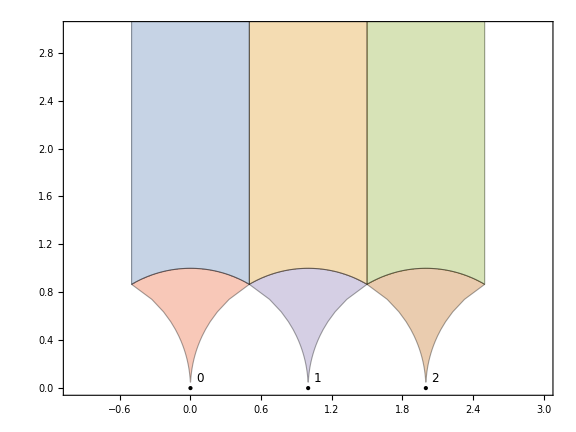

```mathematica
pltback=PlotModularDomain[
{IdMatrix,TMatrix[1],TMatrix[2],SMatrix,TMatrix[1].SMatrix,TMatrix[2].SMatrix},
 "YMax"->20,
PlotRange->{{-1,3},{0,3}},
AspectRatio->Automatic,
"ShowBackground"->True,
"BackgroundMaxLen"->8,
"BackgroundStyle"->{Transparent,EdgeForm[Directive[Gray,Thin]]}]
```

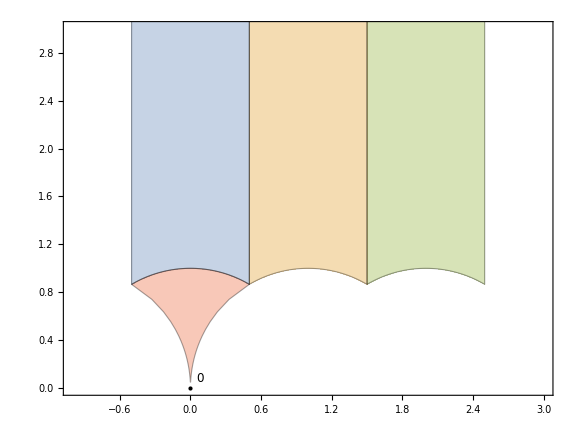

```mathematica
PlotModularDomain[
{IdMatrix,TMatrix[1],TMatrix[2],SMatrix},
 "YMax"->20,
PlotRange->{{-1,3},{0,3}},
AspectRatio->Automatic,
"ShowBackground"->True,
"BackgroundMaxLen"->8,
"BackgroundStyle"->{Transparent,EdgeForm[Directive[Gray,Thin]]}]
```

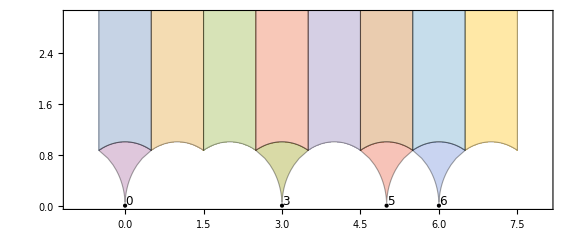

```mathematica
PlotModularDomain[
{IdMatrix,TMatrix[1],TMatrix[2],TMatrix[3],TMatrix[4],TMatrix[5],TMatrix[6],TMatrix[7],SMatrix, TMatrix[3].SMatrix,TMatrix[5].SMatrix, TMatrix[6].SMatrix},
 "YMax"->20,
PlotRange->{{-1,8},{0,3}},
AspectRatio->Automatic,
"ShowBackground"->True,
"BackgroundMaxLen"->8,
"BackgroundStyle"->{Transparent,EdgeForm[Directive[Gray,Thin]]}]
```

```mathematica
Clear[sw1];
sw1[x_,u_]:=x^2(x-u)+1/4m L^3 x-1/64L^6;
```

```mathematica
ClearAll[m,L];
L=1;
```

```mathematica
Simplify[16Discriminant[sw1[x,u],x]]
u0=u/.Solve[%==0,u]
```

-27/256-u^3

{-3/4 (-1/2)^(2/3),-3/(4 2^(2/3)),(3 (-1)^(1/3))/(4 2^(2/3))}

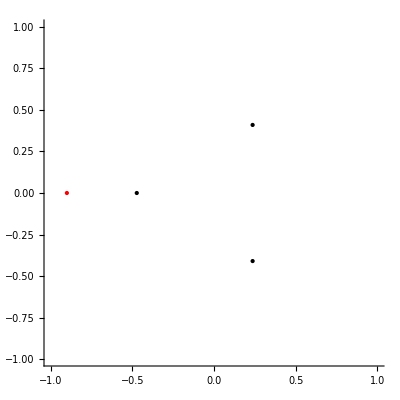

```mathematica
Graphics[{PointSize[Large],Point/@ReIm[u0],Red,Point[ReIm[-.9]]},Axes->True,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
x0=x/.Solve[sw1[x,-.5]==0,x]
```

{-0.404508,-0.25,0.154508}

```mathematica
NIntegrate[Sqrt[2]/(2Pi)(x-(-.5))/Sqrt[sw1[x,-.5]], {x,x0[[1]],x0[[2]]}]
```

0.18004

```mathematica
Simplify[g2^3-27g3^2/.g2g3FromCubic[Collect[sw1[x,u],x],x]]

WeierstrassHalfPeriods[%]/(-3.9510749923970665 ⅈ)
```

-27/256-u^3

(0.+0.253096 ⅈ) WeierstrassHalfPeriods[-27/256-u^3]

```mathematica
0.-1.691894894269601 ⅈ/0.4282112836443912
```

0.-3.95107 ⅈ

```mathematica
WeierstrassHalfPeriods[{1.,2.}]
```

{1.30836+0. ⅈ,0.654182+1.22937 ⅈ}

```mathematica
With[{lam=.5},WeierstrassHalfPeriods[{lam^2 1.,lam^3 2.}]*Sqrt[lam]]
```

{1.30836+0. ⅈ,0.654182+1.22937 ⅈ}

```mathematica
g2g3=g2g3FromCubic[sw1[x,u],x]
```

{g2→-m+(4 u^2)/3,g3→1/16-(m u)/3+(8 u^3)/27}

```mathematica
del=Simplify[g2^3-27g3^2/.g2g3]
```

-27/256-m^3+(9 m u)/8+m^2 u^2-u^3

```mathematica
m0=0;
```

```mathematica
u0=u/.Solve[del==0/.{m->m0},u]
```

{-3/4 (-1/2)^(2/3),-3/(4 2^(2/3)),(3 (-1)^(1/3))/(4 2^(2/3))}

```mathematica
FullSimplify[{g2,g3}/.g2g3/.m->m0/.u->u]
```

{(4 u^2)/3,1/16+(8 u^3)/27}

```mathematica
g2[u_]:=(4 u^2)/3;g3[u_]:=1/16+(8 u^3)/27;
```

```mathematica
FullSimplify[{g2,g3}/.g2g3/.m->m0/.u->u0[[2]]+eps]
```

{1/48 (3 2^(1/3)-8 eps)^2,1/16+8/27 (-3/(4 2^(2/3))+eps)^3}

```mathematica
g2g3p[eps_]:={1/48 (3 2^(1/3)-8 eps)^2,1/16+8/27 (-3/(4 2^(2/3))+eps)^3};
```

```mathematica
With[{eps=1/1000000},N[WeierstrassHalfPeriods[g2g3p[eps/2]]-WeierstrassHalfPeriods[g2g3p[eps]],40]]
```

{-2.015332760222703467532455736192459788613×10^-7+0. ⅈ,-1.00766638011135173376622786809623×10^-7+0.2521024702308006429977244193255138432554 ⅈ}

```mathematica
a1=With[{eps=1/1000000},N[WeierstrassHalfPeriods[g2g3p[eps]],40]][[1]]
```

2.285244402351172371527802154987161369153+0. ⅈ

```mathematica
a2=With[{eps=1/10000000},N[WeierstrassHalfPeriods[g2g3p[eps]],40]][[1]]
```

2.285244039591281929608082500875453871092+0. ⅈ

```mathematica
Zp=(1/1000000a2-1/10000000a1)/(1/1000000-1/10000000)
```

2.285243999284627436061446983751930815752+0. ⅈ

```mathematica
phi=With[{psi=0}, psi-Arg[Zp]+Pi/2]
```

1.570796326794896619231321691639751442099

```mathematica
{ustart,Zstart}=With[{eps=1/1000000},{u0[[2]]+eps Exp[I phi],Zp eps Exp[I phi]}]
```

{-0.472470393710577436787703977729335631463844299+1.×10^-6 ⅈ,0.+2.285243999284627436061446983751930815752×10^-6 ⅈ}

```mathematica
ZPrime[u_]:=WeierstrassHalfPeriods[{g2[u],g3[u]}][[1]];
```

```mathematica
With[{psi=0},NDSolve[{us'[t]==I Exp[I psi]Conjugate[ZPrime[us[t]]],
Z'[t]==ZPrime[us[t]]*us'[t],
us[0]==ustart,
Z[0]==Zstart},{us,Z}, {t,0,.2}]]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mconly: For the method NDSolve`IDA, only machine real code is available. Unable to continue with complex values or beyond floating-point exceptions.

{}

```mathematica
D[WeierstrassHalfPeriods[{g2,g3}],g2]/.{g2->.3,g3->.4}
```

WeierstrassHalfPeriods^({1,0})[{0.3,0.4}]

```mathematica
With[{es=Sqrt[g2[u0[[2]]]/12]},N[Pi/2/Sqrt[3es],40]]
```

2.285243999284629213340045428297997979621

```mathematica
Om12[{e1_,e2_,e3_}]:={EllipticK[(e2-e3)/(e1-e3)]/Sqrt[e1-e3],I EllipticK[(e1-e2)/(e1-e3)]/Sqrt[e1-e3]};
```

```mathematica
Block[{g2=.2-.3I,g3=.4+.4I},{x/.Solve[4x^3-g2 x-g3==0,x], WeierstrassHalfPeriods[{g2,g3}]}]
Om12[%[[1]]]
```

{{-0.424822+0.379883 ⅈ,-0.0970324-0.4599 ⅈ,0.521855+0.0800175 ⅈ},{0.596745-1.52214 ⅈ,1.67163-0.1618 ⅈ}}

{0.596745-1.52214 ⅈ,1.67163-0.1618 ⅈ}

```mathematica
Block[{g2=.2-.3I,g3=.4+.4I},Permutations[x/.Solve[4x^3-g2 x-g3==0,x]]]
TableForm[Om12/@%]
```

{{-0.424822+0.379883 ⅈ,-0.0970324-0.4599 ⅈ,0.521855+0.0800175 ⅈ},{-0.424822+0.379883 ⅈ,0.521855+0.0800175 ⅈ,-0.0970324-0.4599 ⅈ},{-0.0970324-0.4599 ⅈ,-0.424822+0.379883 ⅈ,0.521855+0.0800175 ⅈ},{-0.0970324-0.4599 ⅈ,0.521855+0.0800175 ⅈ,-0.424822+0.379883 ⅈ},{0.521855+0.0800175 ⅈ,-0.424822+0.379883 ⅈ,-0.0970324-0.4599 ⅈ},{0.521855+0.0800175 ⅈ,-0.0970324-0.4599 ⅈ,-0.424822+0.379883 ⅈ}}

0.596745-1.52214 ⅈ | 1.67163-0.1618 ⅈ
0.596745-1.52214 ⅈ | 1.07488+1.36034 ⅈ
1.07488+1.36034 ⅈ | -1.67163+0.1618 ⅈ
1.07488+1.36034 ⅈ | -0.596745+1.52214 ⅈ
1.67163-0.1618 ⅈ | 1.07488+1.36034 ⅈ
1.67163-0.1618 ⅈ | -0.596745+1.52214 ⅈ

```mathematica
1.671629120823785-0.16179990839894734 ⅈ-(0.5967450906171303-1.522135401821424 ⅈ)
```

1.07488+1.36034 ⅈ

```mathematica
plt1=Graphics[{PointSize[Large],Point/@ReIm[u0],Red,Point[ReIm[-.9]]},Axes->True,PlotRange->{{-1,1},{-1,1}}]
```

-Graphics-

```mathematica
{Sqrt[g2[u0[[2]]]/12],-2Sqrt[g2[u0[[2]]]/12]}
```

{1/(4 2^(2/3)),-1/(2 2^(2/3))}

## Claude basic implementation

```mathematica
Clear[sw1,m];
sw1[x_,u_]:=x^2(x-u)+1/4m x-1/64;
```

```mathematica
(* ===================== Parameters ===================== *)
mass = 0;     (* 0 < mass < mAD = 0.75 for Λ1 = 1 *)
ψ    =.3;     (* ray phase *)
sing = 1;       (* which singularity: 1, 2, or 3 *)
ϵ    = 10^-5;   (* initial offset *)
smax = .5;
```

```mathematica
(* =====================Curve data=====================*)
g2[u_]:=(4/3) u^2-mass;
g3[u_]:=(8/27) u^3-(mass/3) u+1/16;
g2p[u_]:=8 u/3;
g3p[u_]:=(8/9) u^2-mass/3;
```

```mathematica
(* =====================Singularities=====================*)Δ1[u_]:=u^3-mass^2 u^2-(9/8) mass u+mass^3+27/256;
usings=u/. NSolve[Δ1[u]==0,u];
uS=usings[[sing]];
```

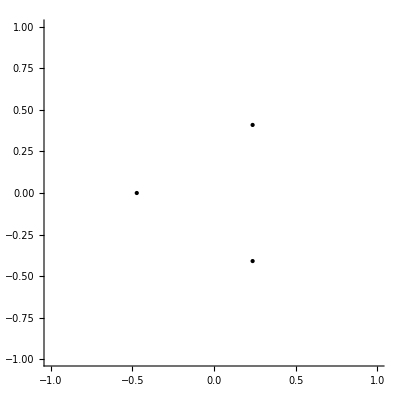

```mathematica
plt1=Graphics[{PointSize[Large],Point/@ReIm[usings]},Axes->True,PlotRange->{{-1,1},{-1,1}}]
```

```mathematica
(*double root e* and closed-form Z'(u_{s,i})*)
e0=Sqrt[g2[uS]/12];
eStar=If[Abs[e0^3+g3[uS]/8]<Abs[(-e0)^3+g3[uS]/8],e0,-e0];
ZpS=(Pi/2)/Sqrt[3 eStar];
```

```mathematica
(* =====================Period-derivative=====================*)modulus[e1_,e2_,e3_]:=(e2-e3)/(e1-e3);
Zprime[e1_,e2_,e3_]:=EllipticK[1-modulus[e1,e2,e3]]/Sqrt[e1-e3];
```

```mathematica
(* =====================Initial conditions=====================*)φ=ψ-Arg[ZpS]+Pi/2;          (*the other ray-direction is-Pi/2*)
u0=uS+ϵ Exp[I φ];
```

```mathematica
cubicRoots=x/. NSolve[4 x^3-g2[u0] x-g3[u0]==0,x];
ordered=SortBy[cubicRoots,Abs[#-eStar]&];
{e1i,e2i,e3i}=ordered;          (*first two are the splitting pair*)
```

```mathematica
Z0=ZpS*ϵ*Exp[I φ];
```

```mathematica
(* =====================ODE system=====================*)uDot[u_,e1_,e2_,e3_]:=I Exp[I ψ] Conjugate[Zprime[e1,e2,e3]];
```

```mathematica
eqs={u'[s]==uDot[u[s],e1[s],e2[s],e3[s]],e1'[s]==(g2p[u[s]] e1[s]+g3p[u[s]])/(12 e1[s]^2-g2[u[s]])*uDot[u[s],e1[s],e2[s],e3[s]],e2'[s]==(g2p[u[s]] e2[s]+g3p[u[s]])/(12 e2[s]^2-g2[u[s]])*uDot[u[s],e1[s],e2[s],e3[s]],e3'[s]==(g2p[u[s]] e3[s]+g3p[u[s]])/(12 e3[s]^2-g2[u[s]])*uDot[u[s],e1[s],e2[s],e3[s]],Z'[s]==Zprime[e1[s],e2[s],e3[s]]*uDot[u[s],e1[s],e2[s],e3[s]],u[0]==u0,e1[0]==e1i,e2[0]==e2i,e3[0]==e3i,Z[0]==Z0};
```

```mathematica
sol=NDSolve[eqs,{u,e1,e2,e3,Z},{s,0,smax},WorkingPrecision->25,MaxSteps->100000][[1]]
```

NDSolve::precw: The precision of the differential equation ({{u'[s]==(-0.29552+0.955336 ⅈ) Conjugate[EllipticK[Plus[«2»]]/(√Plus[«2»])],«8»,Z[0]==-6.75336×10^-6+0.0000218318 ⅈ},{},{},{},{}}) is less than WorkingPrecision (25.).

{u→InterpolatingFunction[…],e1→InterpolatingFunction[…],e2→InterpolatingFunction[…],e3→InterpolatingFunction[…],Z→InterpolatingFunction[…]}

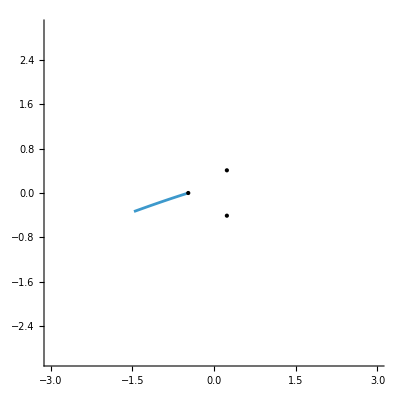

```mathematica
(* =====================Plot in the u-plane=====================*)
With[{len=3},Show[plt1,ParametricPlot[{Re[u[s]],Im[u[s]]}/. sol,{s,0,smax},PlotRange->All,AxesLabel->{"Re u","Im u"},PlotLabel->"BPS ray in u-plane"],PlotRange->{{-len,len},{-len,len}}]]
```

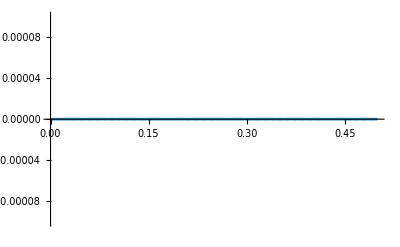

```mathematica
ReImPlot[Arg[Z[s]/.sol]-Pi/2-ψ,{s,0,smax},PlotRange->{Automatic,{-10^-4,10^-4}}]
```

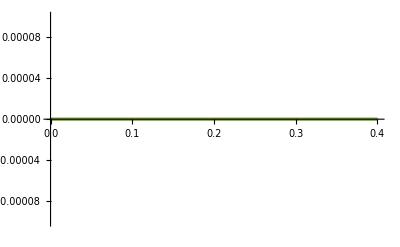

```mathematica
Plot[{Abs[4e1[s]^3-g2[u[s]]e1[s]-g3[u[s]]/.sol], Abs[4e2[s]^3-g2[u[s]]e2[s]-g3[u[s]]/.sol], Abs[4e3[s]^3-g2[u[s]]e3[s]-g3[u[s]]/.sol]},{s,0,.4},PlotRange->{Automatic,{-10^-4,10^-4}}]
```

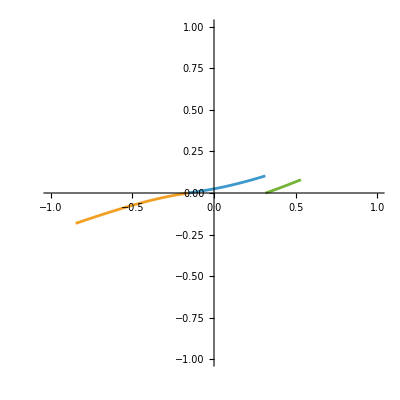

```mathematica
ParametricPlot[{ReIm[e1[s]/.sol],ReIm[e2[s]/.sol],ReIm[e3[s]/.sol]},{s,0,.4},PlotRange->{{-1,1},{-1,1}}]
```

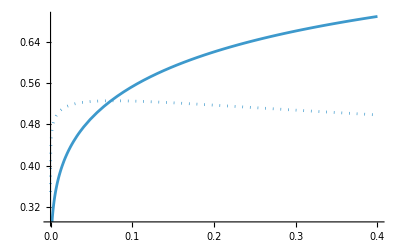

```mathematica
ReImPlot[τ[s]/.sol,{s,0,.4}]
```

```mathematica
(* =====================Map to τ and plot=====================*)τ[s_]:=I EllipticK[1-modulus[e1[s],e2[s],e3[s]]]/EllipticK[modulus[e1[s],e2[s],e3[s]]]/. sol;
```

Show::gcomb: Could not combine the graphics objects in Show[,pltback].

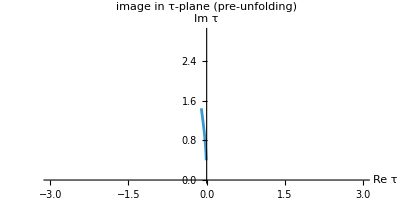
Show[-Graphics-,pltback]

```mathematica
With[{n=1},Show[ParametricPlot[ReIm[τ[s]/(-n τ[s]+1)],{s,0,.4},PlotRange->{{-3,3},{0,3}},AxesLabel->{"Re τ","Im τ"},PlotLabel->"image in τ-plane (pre-unfolding)"], pltback]]
```

```mathematica
MatrixPower[{{1,0},{-1,1}},n]
```

{{1,0},{-n,1}}

```mathematica
ClearAll[ArcLengthReparametrize];

ArcLengthReparametrize[f_,{smin_?NumericQ,smax_?NumericQ},n_Integer:10000,metric_:"Euclidean"]:=Module[{sGrid,zGrid,increments,lengthGrid,tolerance,keep,sOfLength,totalLength},sGrid=Subdivide[N[smin],N[smax],n];
zGrid=f/@sGrid;
If[!VectorQ[zGrid,NumericQ],Print["The function did not return numerical values everywhere."];
Return[$Failed]];
increments=Switch[metric,"Euclidean",Abs[Differences[zGrid]],"Hyperbolic",Abs[Differences[zGrid]]/((Im[Most[zGrid]]+Im[Rest[zGrid]])/2),_,Print["Metric must be \"Euclidean\" or \"Hyperbolic\"."];
Return[$Failed]];
lengthGrid=Prepend[Accumulate[increments],0.];
(*Remove numerically stationary points so that inversion is possible*)tolerance=10^-12 Max[1.,Last[lengthGrid]];
keep=Prepend[Flatten[Position[Differences[lengthGrid],x_/;x>tolerance]]+1,1];
keep=DeleteDuplicates[keep];
sOfLength=Interpolation[Transpose[{lengthGrid[[keep]],sGrid[[keep]]}],InterpolationOrder->1];
totalLength=Last[lengthGrid[[keep]]];
<|"TotalLength"->totalLength,"OriginalParameter"->sOfLength,"Curve"->Function[{ℓ},f[sOfLength[ℓ]]]|>]
```

```mathematica
rp=ArcLengthReparametrize[τ,{0,smax},20000,"Hyperbolic"];
```

```mathematica
tauArc[ℓ_?NumericQ]:=rp["Curve"][ℓ];
```

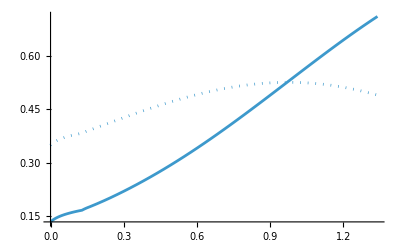

```mathematica
ReImPlot[tauArc[l],{l,0,rp["TotalLength"]}]
```

Show::gcomb: Could not combine the graphics objects in Show[,pltback].

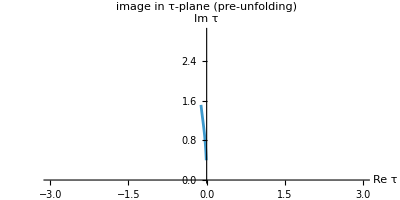
Show[-Graphics-,pltback]

```mathematica
With[{n=1},Show[ParametricPlot[ReIm[tauArc[l]/(-n tauArc[l]+1)],{l,0,rp["TotalLength"]},PlotRange->{{-3,3},{0,3}},AxesLabel->{"Re τ","Im τ"},PlotLabel->"image in τ-plane (pre-unfolding)"], pltback]]
```

## scratch

```mathematica
FullSimplify[ComplexExpand[Im[-1/(t1+I t2-ts)]]]
```

t2/(t2^2+(t1-ts)^2)

```mathematica
(e2-e3)/(e1-e3)
```

(e2-e3)/(e1-e3)

```mathematica
FullSimplify[Abs[D[I EllipticK[1-m]/EllipticK[m],m]]]
```

1/2 Abs[(EllipticK[1-m] (EllipticE[m]-EllipticK[m])+EllipticE[1-m] EllipticK[m])/((-1+m) m EllipticK[m]^2)]

```mathematica
With[{u=-100},x/.Solve[4x^3-g2[u]x-g3[u]==0,x]]
```

{-66.6659,33.3205,33.3455}

```mathematica
N[2/3(-100)+mass/4/(-100)]
```

-66.6674

```mathematica
4x^3-g2 x-g3/.{g2->-m+(4 u^2)/3,g3->1/16-(m u)/3+(8 u^3)/27}
Series[%,{u,-Infinity,2}]
```

-1/16+(m u)/3-(8 u^3)/27-(-m+(4 u^2)/3) x+4 x^3

-(8 u^3)/27-(4 x u^2)/3+(m u)/3+(-1/16+m x+4 x^3)+O[1/u]^3

```mathematica
Assuming[{0<m<3/4,u<0},FullSimplify[Series[x/.First[Solve[-1/16+(m u)/3-(8 u^3)/27-(-m+(4 u^2)/3) x+4 x^3==0,x]], {u,-Infinity,4}]]]
```

(2 u)/3-m/(4 u)+1/(64 u^2)-m^2/(16 u^3)+(3 m)/(256 u^4)+O[1/u]^(9/2)

```mathematica
Assuming[{0<m<3/4,u<0},FullSimplify[Series[x/.Solve[-1/16+(m u)/3-(8 u^3)/27-(-m+(4 u^2)/3) x+4 x^3==0,x][[2]], {u,-Infinity,4}]]]
```

-u/3-1/8 ⅈ √(1/u)+m/(8 u)+1/16 ⅈ m^2 (1/u)^(3/2)-1/(128 u^2)+1/128 ⅈ m (-3+2 m^3) (1/u)^(5/2)+m^2/(32 u^3)+(ⅈ (5+80 m^3+32 m^6) (1/u)^(7/2))/4096-(3 m)/(512 u^4)+O[1/u]^(9/2)

```mathematica
Assuming[{0<m<3/4,u<0},FullSimplify[Series[(x-u)/Sqrt[-1/16+(m u)/3-(8 u^3)/27-(-m+(4 u^2)/3) x+4 x^3],{u,-Infinity,3}]]]
Assuming[{0<m<3/4,u<0},FullSimplify[Series[Integrate[Sqrt[2]/(2Pi)%,{x,(2 u)/3-m/(4 u),-u/3-1/8 ⅈ √(1/u)}],{u,-Infinity,4}]]]
```

3/2 ⅈ √(3/2) √(1/u)-39/8 ⅈ √(3/2) x (1/u)^(3/2)+27/64 ⅈ √(3/2) (2 m+35 x^2) (1/u)^(5/2)+O[1/u]^(7/2)

-(149 ⅈ √3 √u)/(128 π)-(305 √3)/(1024 π u)+(23 ⅈ √3 m (1/u)^(3/2))/(128 π)+(471 ⅈ √3 (1/u)^(5/2))/(8192 π)-(27 (√3 m))/(512 π u^3)-(129 ⅈ √3 m^2 (1/u)^(7/2))/(1024 π)+(315 √3)/(65536 π u^4)+O[1/u]^(9/2)

```mathematica
Solve[(x^2-1)(x-u)==0,x]
```

{{x→-1},{x→1},{x→u}}

```mathematica
Assuming[u>1,Simplify[Series[Integrate[(x-u)/Sqrt[(x^2-1)(x-u)],{x,-1,1}],{u,Infinity,1}]]]
```

$Aborted

```mathematica
Assuming[u>0,Simplify[Series[(x-u)/Sqrt[(x^2-1)(x-u)], {u,Infinity,2}]]]
Assuming[u>0,Simplify[Series[Integrate[Sqrt[2]/(2Pi)%,{x,-1,1}],{u,Infinity,2}]]]
```

-(√u)/(√(1-x^2))+(x √(1/u))/(2 √(1-x^2))+(x^2 (1/u)^(3/2))/(8 √(1-x^2))+O[1/u]^(5/2)

-(√u)/(√2)+(1/u)^(3/2)/(16 √2)+O[1/u]^(5/2)

```mathematica
Assuming[u>0,Simplify[Series[(x-u)/Sqrt[(x^2-1)(x-u)], {u,Infinity,2}]]]
Assuming[u>0,Simplify[Series[Integrate[Sqrt[2]/(2Pi)%,{x,1,u}],{u,Infinity,2}]]]
D[%,u]/D[-(√u)/(√2)+(1/u)^(3/2)/(16 √2)+O[1/u]^(5/2),u]
```

-(√u)/(√(1-x^2))+(x √(1/u))/(2 √(1-x^2))+(x^2 (1/u)^(3/2))/(8 √(1-x^2))+O[1/u]^(5/2)

(ⅈ (-9+16 Log[2]+16 Log[u]) √u)/(16 √2 π)-(ⅈ (-1+Log[4]+2 Log[u]) (1/u)^(3/2))/(32 √2 π)+O[1/u]^(5/2)

-(ⅈ (23+16 Log[2]+16 Log[u]))/(16 π)+(-(ⅈ (-7+3 Log[4]+6 Log[u]))/(32 π)+(3 ⅈ (23+16 Log[2]+16 Log[u]))/(256 π))/u^2+O[1/u]^3

```mathematica
Solve[-(√u)/(√2)==a,u]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{u→2 a^2}}

```mathematica
Simplify[FullSimplify[-(ⅈ (23+16 Log[2]+16 Log[u]))/(16 π)]/.{u->2 a^2},a>1]
```

-(ⅈ (23+16 Log[4 a^2]))/(16 π)

## Picard Fuchs

```mathematica
(* taken from Huang Klemm 09: 0902.1325 *)
```

```mathematica
PF[f_,u_,m_]:=(-8 (9 m+32 m^4-72 m^2 u+24 u^2) D[f,u]+(81+768 m^3-864 m u-768 m^2 u^2+768 u^3+32 (4 m^2-3 u) (24 m^2-9 u-16 m u^2)) D[f,{u,2}]+(4 m^2-3 u) (27+256 m^3-288 m u-256 m^2 u^2+256 u^3) D[f,{u,3}])/((4 m^2-3 u) (27+256 m^3-288 m u-256 m^2 u^2+256 u^3));
```

```mathematica
Coefficient[PF[f[u],u,m], D[f[u],u]]
```

-(8 (9 m+32 m^4-72 m^2 u+24 u^2))/((4 m^2-3 u) (27+256 m^3-288 m u-256 m^2 u^2+256 u^3))

```mathematica
Simplify[With[{a=-2 2^(1/3),b=1/(2 2^(1/3)),c=1/2^(2/3)},Simplify[{a^2g2,a^3g3}/.g2g3FromCubic[sw1[x,u],x]/.{u->u b, m->m c}]]]
```

{-4 m+(4 u^2)/3,-1+(4 m u)/3-(8 u^3)/27}

```mathematica
Solve[4 m^2-3 u==0,u]
```

{{u→(4 m^2)/3}}

```mathematica
FullSimplify[27+256 m^3-288 m u-256 m^2 u^2+256 u^3/.{m->3/4}]
```

(3-4 u)^2 (15+16 u)

```mathematica
Simplify[Series[PF[u^s,u,m]/u^s,{u,-Infinity,3}]]
```

(s (13/4+2 m-2 (2+m) s+s^2))/u^3+O[1/u]^4

```mathematica
Solve[s (13/4+2 m-2 (2+m) s+s^2)==0,s]
```

{{s→0},{s→1/2 (4+2 m-√(3+8 m+4 m^2))},{s→1/2 (4+2 m+√(3+8 m+4 m^2))}}

```mathematica
Simplify[PF[f[u],u,m]/.f->Function[u,ft[1/u]]/.{u->1/w}]
FullSimplify[Series[%/.ft->Function[w,w^s], {w,0,4}]]
```

(w^4 (8 (24-72 m^2 w+9 m w^2+32 m^4 w^2) ft'[w]+(768-768 m^2 w-864 m w^2+81 w^3+768 m^3 w^3+32 (3-4 m^2 w) (16 m+9 w-24 m^2 w^2)) (2 ft'[w]+w ft''[w])-(-3+4 m^2 w) (256-256 m^2 w-288 m w^2+27 w^3+256 m^3 w^3) (6 ft'[w]+w (6 ft''[w]+w ft^(3)[w]))))/((-3+4 m^2 w) (256-256 m^2 w-288 m w^2+27 w^3+256 m^3 w^3))

w^s (-1/4 (s (13+8 m (1+s)+4 s (4+s))) w^3-1/24 (s (27 (1+s)+4 m^2 (7+8 s+12 m (1+s)))) w^4+O[w]^5)

```mathematica
Solve[s (13+8 m (1+s)+4 s (4+s))==0,s]
```

{{s→0},{s→1/2 (-4-2 m-√(3+8 m+4 m^2))},{s→1/2 (-4-2 m+√(3+8 m+4 m^2))}}

```mathematica
pi=Sqrt[u](1+a1 u+a2 u^2+a3 u^3+a4 u^4);
```

```mathematica
Series[PF[pi,u,m],{u,0,1}]
```

3/(8 u^(5/2))-(3 (27+54 a1 m^2+256 m^3+1024 m^4+512 a1 m^5))/(16 (m^2 (27+256 m^3)) u^(3/2))+1/(√u)(-3/8 (135+108 a1 m^2+2432 m^3+2048 m^4+1024 a1 m^5) (72/(m (27+256 m^3)^2)+3/(16 m^4 (27+256 m^3)))+3/2 m^2 (27+256 m^3) (54/(m^3 (27+256 m^3)^2)+9/(64 m^6 (27+256 m^3))+(64 (351+256 m^3))/((27+256 m^3)^3))+1/(4 m^2 (27+256 m^3))(216 m (1+4 m)-4 m (9+32 m^3)+15/2 a2 m^2 (27+256 m^3)+3/8 (864 m-1024 m^4)+3/4 a1 (81+768 m^3+3072 m^4)-3/8 a1 (-1152 m^3-3 (27+256 m^3))))+(-3/8 (135+108 a1 m^2+2432 m^3+2048 m^4+1024 a1 m^5) (54/(m^3 (27+256 m^3)^2)+9/(64 m^6 (27+256 m^3))+(64 (351+256 m^3))/((27+256 m^3)^3))+3/2 m^2 (27+256 m^3) (81/(2 m^5 (27+256 m^3)^2)+27/(256 m^8 (27+256 m^3))+(48 (351+256 m^3))/(m^2 (27+256 m^3)^3)+(64 (-729+95040 m^3+81920 m^6))/(m^2 (27+256 m^3)^4))+(72/(m (27+256 m^3)^2)+3/(16 m^4 (27+256 m^3))) (216 m (1+4 m)-4 m (9+32 m^3)+15/2 a2 m^2 (27+256 m^3)+3/8 (864 m-1024 m^4)+3/4 a1 (81+768 m^3+3072 m^4)-3/8 a1 (-1152 m^3-3 (27+256 m^3)))+1/(4 m^2 (27+256 m^3))(672 m^2-648 a1 m (1+4 m)+8 (-27+24 m^2+64 m^3)+105/2 a3 m^2 (27+256 m^3)-12 m (9 a1-24 m+32 a1 m^3)-3/8 a1 (864 m-1024 m^4)+15/4 a2 (81+768 m^3+3072 m^4)+15/8 a2 (-1152 m^3-3 (27+256 m^3)))) √u+O[u]^(3/2)

## Integrating from LV down to cusps

```mathematica
Delta1[m_]:=27 Lambda1^6+256 Lambda1^3 m^3-288 Lambda1^3 m u-256 m^2 u^2+256 u^3;
```

```mathematica
op[Pi1_]:=D[Pi1[u],{u,3}]+((3 Delta1[m]+Delta1'[m] (4 m^2-3 u))/(Delta1[m] (4 m^2-3 u))) D[Pi1[u],{u,2}]-(8 (4 (2 m^2-3 u) (4 m^2-3 u)+3 (3 Delta1[m]^3 m-4 u^2))/(Delta1[m] (4 m^2-3 u))) D[Pi1[u],u];
```

```mathematica
Simplify[op[f]/.f->Function[u,ft[-1/u]]/.u->-1/w]
Simplify[Series[%/w^s/.ft->Function[w,w^s], {w,0,1}]]
```

6 w^4 ft'[w]-(8 (4 w^7 (3+2 m^2 w) (3+4 m^2 w)-3 (4 w^7-3 m (-256-256 m^2 w+288 Lambda1^3 m w^2+27 Lambda1^6 w^3+256 Lambda1^3 m^3 w^3)^3)) ft'[w])/(w^3 (3+4 m^2 w) (-256-256 m^2 w+288 Lambda1^3 m w^2+27 Lambda1^6 w^3+256 Lambda1^3 m^3 w^3))+4 w^5 ft''[w]+(w^4 (-768+864 Lambda1^3 w+81 Lambda1^6 w^3+3072 Lambda1^3 m^4 w^3+384 m^2 w (-2+9 Lambda1^3 w)+256 m^3 w (-8+3 Lambda1^3 w^2)+96 m (-16+9 Lambda1^3 w^2)) (2 ft'[w]+w ft''[w]))/((3+4 m^2 w) (-256-256 m^2 w+288 Lambda1^3 m w^2+27 Lambda1^6 w^3+256 Lambda1^3 m^3 w^3))+w^5 (2 ft''[w]+w ft^(3)[w])

-(1572864 (m s))/w^4-(1048576 (m^3 s))/w^3+(131072 (81 Lambda1^3 m^2-4 m^5) s)/(3 w^2)+(4096 (729 Lambda1^6 m+4320 Lambda1^3 m^4+512 m^7) s)/(9 w)-4096/27 ((13851 Lambda1^6 m^3-3456 Lambda1^3 m^6+2048 m^9) s)+512/81 m^2 (-59049 Lambda1^9-116640 Lambda1^6 m^3-110592 Lambda1^3 m^6+65536 m^9) s w+O[w]^2

```mathematica
(* last attempt *)
expr=Simplify[With[{D1=256u^3-256m^2u^2-288L^3m u+256L^3m^3+27L^6},D[f[u],{u,3}]+(3D1+(4m^2-3u)D[D1,u])/(D1(4m^2-3u))D[f[u],{u,2}]-8(4(2m^2-3u)(4m^2-3u)+3(3L^3m-4u^2))/(D1(4m^2-3u))D[f[u],u]]]
```

(-8 (9 L^3 m+8 (4 m^4-9 m^2 u+3 u^2)) f'[u]+(81 L^6-384 L^3 m^3-256 u (8 m^4-15 m^2 u+6 u^2)) f''[u]+(4 m^2-3 u) (27 L^6+256 u^2 (-m^2+u)+32 L^3 (8 m^3-9 m u)) f^(3)[u])/((4 m^2-3 u) (27 L^6+256 u^2 (-m^2+u)+32 L^3 (8 m^3-9 m u)))

```mathematica
Simplify[expr/.f->Function[u,ft[1/u]]/.u->1/w]
Series[%/w^s/.ft->Function[w,w^s],{w,0,1}]
```

(w (8 (24-72 m^2 w+9 L^3 m w^2+32 m^4 w^2) ft'[w]+(-1536+3840 m^2 w-2048 m^4 w^2+81 L^6 w^3-384 L^3 m^3 w^3) (2 ft'[w]+w ft''[w])-(-3+4 m^2 w) (256-256 m^2 w-288 L^3 m w^2+27 L^6 w^3+256 L^3 m^3 w^3) (6 ft'[w]+w (6 ft''[w]+w ft^(3)[w]))))/((-3+4 m^2 w) (27 L^6-(256 (-1+m^2 w))/w^3+(32 L^3 m (-9+8 m^2 w))/w))

-1/4 (s (1+2 s)^2) w^3+O[w]^4

```mathematica
ClearAll[SWLogSeriesCoefficients];

SWLogSeriesCoefficients[nmax_Integer?NonNegative,m_,L_]:=Module[{a,b,K0,K1,K2,K3,K4,S0,S1,S2,S3,S4,get},a=ConstantArray[0,nmax+1];
b=ConstantArray[0,nmax+1];
a[[1]]=1;(*a_0*)b[[1]]=0;(*b_0 normalization*)get[arr_,k_]:=If[k<0||k>nmax,0,arr[[k+1]]];
K0[n_]:=384 n^2 (2 n-1);
K1[n_]:=-128 m^2 (n-1) (2 n-3) (7 n-8);
K2[n_]:=16 m (2 n-5) (-27 L^3 n^2+54 L^3 n-18 L^3+32 m^3 n^2-128 m^3 n+128 m^3);
K3[n_]:=(3 L^3/8) (2 n-7) (2 n-5) (54 L^3 n-27 L^3+1280 m^3 n-2176 m^3);
K4[n_]:=-(L^3 m^2/2) (27 L^3+256 m^3) (2 n-9) (2 n-7) (2 n-5);
S0[n_]:=-768 n (3 n-1);
S1[n_]:=128 m^2 (42 n^2-102 n+61);
S2[n_]:=-32 m (-81 L^3 n^2+243 L^3 n-153 L^3+96 m^3 n^2-416 m^3 n+448 m^3);
S3[n_]:=-(3 L^3/4) (324 L^3 n^2-1404 L^3 n+1269 L^3+7680 m^3 n^2-39424 m^3 n+48512 m^3);
S4[n_]:=L^3 m^2 (27 L^3+256 m^3) (12 n^2-84 n+143);
(*First compute a_n*)Do[a[[n+1]]=Simplify[-(K1[n] get[a,n-1]+K2[n] get[a,n-2]+K3[n] get[a,n-3]+K4[n] get[a,n-4])/K0[n]],{n,1,nmax}];
(*Then compute b_n*)Do[b[[n+1]]=Simplify[-(K1[n] get[b,n-1]+K2[n] get[b,n-2]+K3[n] get[b,n-3]+K4[n] get[b,n-4]+S0[n] get[a,n]+S1[n] get[a,n-1]+S2[n] get[a,n-2]+S3[n] get[a,n-3]+S4[n] get[a,n-4])/K0[n]],{n,1,nmax}];
<|"a"->a,"b"->b|>]
```

```mathematica
ClearAll[mu,logseries,logseriesTemplate];
logseriesTemplate=SWLogSeriesCoefficients[100,mu,1];
logseries[mval_]:=logseriesTemplate/. mu->mval;
```

```mathematica
Series[Sqrt[u]Total[logseries[m]["a"]/u^Range[0,Length[logseries[m]["a"]]-1]], {u,Infinity,10}]
Simplify[expr/.{L->1}/.f->Function[u,Evaluate[%]]]
```

√u-1/16 m (1/u)^(3/2)+(3 (1/u)^(5/2))/1024-(15 m^2 (1/u)^(7/2))/1024+(35 m (1/u)^(9/2))/16384-(105 (3+256 m^3) (1/u)^(11/2))/4194304+(3465 m^2 (1/u)^(13/2))/2097152-(3003 (m (3+80 m^3)) (1/u)^(15/2))/67108864+(15015 (1+384 m^3) (1/u)^(17/2))/4294967296-(153153 (m^2 (5+64 m^3)) (1/u)^(19/2))/4294967296+O[1/u]^(21/2)

O[1/u]^(27/2)

```mathematica
Series[Sqrt[u]Total[logseries[m]["a"]/u^Range[0,Length[logseries[m]["a"]]-1]]Log[u]+Sqrt[u]Total[logseries[m]["b"]/u^Range[0,Length[logseries[m]["a"]]-1]], {u,Infinity,10}];
Simplify[expr/.{L->1}/.f->Function[u,Evaluate[%]]]
```

O[1/u]^(27/2)

```mathematica
With[{Cc=x^2-u,G=L^3(x+m)},Cc^2-G]
sols=Assuming[{u<0,L>0},Simplify[Series[x/.Solve[%==0,x],{u,-Infinity,3}]]]
```

-L^3 (m+x)+(-u+x^2)^2

{-√u-1/2 ⅈ L^(3/2) (1/u)^(1/4)+1/4 ⅈ L^(3/2) m (1/u)^(3/4)+1/16 ⅈ L^(3/2) m^2 (1/u)^(5/4)+1/8 L^3 m (1/u)^(3/2)-1/64 ⅈ L^(3/2) (L^3-2 m^3) (1/u)^(7/4)-5/256 ⅈ L^(3/2) (2 L^3 m-m^4) (1/u)^(9/4)-1/128 L^6 (1/u)^(5/2)+7/512 ⅈ L^(3/2) (3 L^3 m^2+m^5) (1/u)^(11/4)+O[1/u]^(13/4),-√u+1/2 ⅈ L^(3/2) (1/u)^(1/4)-1/4 ⅈ L^(3/2) m (1/u)^(3/4)-1/16 ⅈ L^(3/2) m^2 (1/u)^(5/4)+1/8 L^3 m (1/u)^(3/2)+1/64 ⅈ L^(3/2) (L^3-2 m^3) (1/u)^(7/4)+5/256 ⅈ L^(3/2) (2 L^3 m-m^4) (1/u)^(9/4)-1/128 L^6 (1/u)^(5/2)-7/512 ⅈ L^(3/2) (3 L^3 m^2+m^5) (1/u)^(11/4)+O[1/u]^(13/4),√u-1/2 L^(3/2) (1/u)^(1/4)-1/4 (L^(3/2) m) (1/u)^(3/4)+1/16 L^(3/2) m^2 (1/u)^(5/4)-1/8 (L^3 m) (1/u)^(3/2)+1/64 L^(3/2) (L^3-2 m^3) (1/u)^(7/4)-5/256 (L^(3/2) (2 L^3 m-m^4)) (1/u)^(9/4)+1/128 L^6 (1/u)^(5/2)-7/512 (L^(3/2) (3 L^3 m^2+m^5)) (1/u)^(11/4)+O[1/u]^(13/4),√u+1/2 L^(3/2) (1/u)^(1/4)+1/4 L^(3/2) m (1/u)^(3/4)-1/16 (L^(3/2) m^2) (1/u)^(5/4)-1/8 (L^3 m) (1/u)^(3/2)-1/64 (L^(3/2) (L^3-2 m^3)) (1/u)^(7/4)+5/256 L^(3/2) (2 L^3 m-m^4) (1/u)^(9/4)+1/128 L^6 (1/u)^(5/2)+7/512 L^(3/2) (3 L^3 m^2+m^5) (1/u)^(11/4)+O[1/u]^(13/4)}

```mathematica
With[{Cc=x^2-u,G=L^3(x+m)},Module[{y=Sqrt[Cc^2-G]},Simplify[Sqrt[2]/(4Pi I)x/y(Cc D[G,x]/(2G)-D[Cc,x])]]]
```

(ⅈ x (u+x (4 m+3 x)))/(4 √2 π (m+x) √(-L^3 (m+x)+(u-x^2)^2))

```mathematica
Simplify[Series[(ⅈ x (u+x (4 m+3 x)))/(4 √2 π (m+x) √(-L^3 (m+x)+(u-x^2)^2)),{u,Infinity,3}]]
Integrate[Normal[%],x]
Assuming[{u<0,L>0},Simplify[1/((389 ⅈ)/(210 √2 π))Series[(%/.{x->Normal[sols[[4]]]})-(%/.{x->Normal[sols[[1]]]}), {u,-Infinity,1}]]]
(*Integrate[Normal[%],{x,Normal[sols[[1]]],Normal[sols[[2]]]}]*)
```

(ⅈ x)/(4 √2 π (m+x))+(ⅈ x^2)/(√2 π u)+(ⅈ x (L^3+8 x^3))/(8 √2 π u^2)+(ⅈ x^2 (4 x^4+L^3 (2 m+3 x)))/(4 √2 π u^3)+O[1/u]^4

(ⅈ (2 u^3 x+1/2 L^3 u x^2+4/3 (L^3 m+2 u^2) x^3+(3 L^3 x^4)/2+(8 u x^5)/5+(8 x^7)/7-2 m u^3 Log[m+x]))/(8 √2 π u^3)

√u-105/778 ⅈ m π+(1365/1556+(1365 ⅈ)/1556) L^(3/2) (1/u)^(1/4)-105/389 m^2 √(1/u)+(1155/3112-(1155 ⅈ)/3112) L^(3/2) m (1/u)^(3/4)+O[1/u]^(5/4)

```mathematica
With[{Cc=x^2-u,G=L^3(x+m)},Cc^2-G]/.L->1
%/.{L->1,m->1,u->100}
x/.Solve[%==0,x]
```

-m-x+(-u+x^2)^2

-1-x+(-100+x^2)^2

{,,,}

```mathematica
-1-x+(-u+x^2)^2/.{x->#}
```

-1-#1+(-u+#1^2)^2

```mathematica
rt[u_,i_]:=Root[-1-#1+(-u+#1^2)^2&,i];
```

```mathematica
rt[4,1]
```

```mathematica
With[{sc=11},Manipulate[Graphics[{Red,PointSize[.02],Point[ReIm/@{rt[u1+I u2,1], rt[u1+I u2,2], rt[u1+I u2,3], rt[u1+I u2,4]}]}, Axes->True,PlotRange->{{-sc,sc},{-sc,sc}}],{u1,-10,10,.1},{u2,-10,10,.1}]]
```

```mathematica
period[m_,u_,L_,{i_,j_}]:=Module[{x0,x},
x0=x/.NSolve[-L^3 (m+x)+(u-x^2)^2==0,x];
NIntegrate[(ⅈ x (u+x (4 m+3 x)))/(4 √2 π (m+x) √(-L^3 (m+x)+(u-x^2)^2)),{x,x0[[i]],x0[[j]]},WorkingPrecision->40,AccuracyGoal->90,PrecisionGoal->10]];
```

```mathematica
Table[period[1,100,1,op],{op,Subsets[Range[4],{2}]}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$143394 near {x$143394} = {9.83404741608498774157105230087882984937526536613706804079201674245611526418795229728981998-3.1601155336163345580144502805922631914799548021634191500197269426505851778542044414419266×10^-16 ⅈ}. NIntegrate obtained -1.59097852972742458716851041787661001698007004041635958634964760554279124010964549544194973+9.07245767234190239066948809433489179452624664759843362408366598506251676628918940070963634 ⅈ and 3.61503002403045223277962083422151638734959256453474560214149177114792296880811627451875848×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$143430 near {x$143430} = {9.97893260747406209321243210908987768741563900758681394028299703844837310048432412509798497-0.0013893302408926806436359117073414207618227764919867261991325017066325032261119594576778372 ⅈ}. NIntegrate obtained -1.61313930591633166613023130503279525122817273167859104122960407919603503913601731352776339+9.05584975079548716759521500601794965389523845748720152988969493110329150399100340194404489 ⅈ and 0.0116361920012278828347327447270364088076879247608102912701636086303006379267755008138499112 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x$143469 near {x$143469} = {9.83404741608498774157105230087882984937526536613706804079201674245611526418795229728981998+3.1601155336163345580144502805922631914799548021634191500197269426505851778542044414419266×10^-16 ⅈ}. NIntegrate obtained 1.59097852972742458716851041787661001698007004041635958634964760554279124010964549544194973+9.07245767234190239066948809433489179452624664759843362408366598506251676628918940070963634 ⅈ and 3.61503002403045223277962083422151638734959256453474560214149177114792296880811627451980936×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

{-3.535510815928892324812765347387041688009+0. ⅈ,-1.59097852972742458716851041787661001698+9.072457672341902390669488094334891794526 ⅈ,-1.61313930591633166613023130503279525123+9.055849750795487167595215006017949653895 ⅈ,1.59097852972742458716851041787661001698+9.072457672341902390669488094334891794526 ⅈ,1.61313930591633166613023130503279525123+9.055849750795487167595215006017949653895 ⅈ,3.535511364115836630346108207041854723382+1.06266406381599901459674410250018×10^-6 ⅈ}

```mathematica
a1[m_,u_,Nr_]:=Sqrt[u]RichardsonResum[Accumulate[logseries[m]["a"]/u^Range[0,Length[logseries[m]["a"]]-1]], Nr];
a2[m_,u_,Nr_]:=a1[m,u,Nr]Log[u]+Sqrt[u]RichardsonResum[Accumulate[logseries[m]["b"]/u^Range[0,Length[logseries[m]["a"]]-1]], Nr];
```

```mathematica
-L^3 (m+x)+(u-x^2)^2/.{L->1,m->1,u->20Exp[2Pi I t]}
```

-1-x+(20 ⅇ^(2 ⅈ π t)-x^2)^2

```mathematica
roots=AnalyticContinuationOfRoots[-1-x+(20 ⅇ^(2 ⅈ π t)-x^2)^2,x,t,0,1];
```

```mathematica
Keys[roots]
```

{tValues,rootsPaths,finalRoots,initialRoots}

```mathematica
roots["rootsPaths"][[1,1]]
```

-4.47074-0.208448 ⅈ

```mathematica
FullSimplify[(ⅈ x (u+x (4 m+3 x)))/(4 √2 π (m+x) √(-L^3 (m+x)+(u-x^2)^2))/.{L->1,m->1,u->20Exp[2Pi I t]}]
```

(ⅈ x (20 ⅇ^(2 ⅈ π t)+x (4+3 x)))/(4 √2 π (1+x) √(-1-x+(-20 ⅇ^(2 ⅈ π t)+x^2)^2))

```mathematica
data=Monitor[Table[Table[Module[{t},
NIntegrate[(ⅈ x (20 ⅇ^(2 ⅈ π t)+x (4+3 x)))/(4 √2 π (1+x) √(-1-x+(-20 ⅇ^(2 ⅈ π t)+x^2)^2))/.{t->roots["tValues"][[r]]},{x,roots["rootsPaths"][[s[[1]],r]],roots["rootsPaths"][[s[[2]],r]]},WorkingPrecision->40,AccuracyGoal->90,PrecisionGoal->10]], {s,Subsets[Range[4],{2}]}],{r, 1, Length[roots["tValues"]]}], ProgressIndicator[r/Length[roots["tValues"]]]];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-4.47074169612390992512018783600069582462310791015625-0.208447707000255843248708191856684745312461148077436480723042469437673179968775156325127783 ⅈ}. NIntegrate obtained -1.58089227200040585313815236170987323569943743783751496225518786947316519454972452873268408+2.34908782477669872449074014624247787637745054772894621310513422766911741055959798409595804×10^-8 ⅈ and 7.73608275273087217815913849716252221070502597849410167777191864337148756730714608684031739×10^-8 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.20923104691861064104822070787905022330779631466745638173335335342453227393195359117394345-4.39128205213771530651296871308916338549910463480036149794439937791547287146051313524937733×10^-16 ⅈ}. NIntegrate obtained -0.613669395251364176837101779697290460261444430051246592381830682970805833798578969880354046+2.83163583423801126226959379586530263589272867142187915503170931400686173077517198937977357 ⅈ and 1.99460209866713961027817693707403461310838366789168237253895503038236252131832949769402597×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.46803089606166682838006614889754527639390301938180789935801599663736944808436005689655965-0.00598461272517314375785623416973610644786386596231940784088833412667485451764975553051352841 ⅈ}. NIntegrate obtained -0.646872298322418469429251279544363627875089403606044454826549080682713199062363166765513548+2.80949320569583857923071875754798868702196126767575652135710452245496905338312873562294399 ⅈ and 0.00474216361967395825508019920218409693509412340767685555209893720861837837500208798037497576 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{-4.47074,-0.208448},{-4.47074,0.208448},{4.20923,0},{4.73225,0}}

```mathematica
With[{sc=6},Manipulate[Graphics[{Red,PointSize[.02],Point[ReIm/@roots["rootsPaths"][[All,r]]],Black,Thickness[.003],Table[Line[ReIm/@{roots["rootsPaths"][[s[[1]],r]], roots["rootsPaths"][[s[[2]],r]]}], {s,Subsets[Range[4],{2}]}]}, Axes->True,PlotRange->{{-sc,sc},{-sc,sc}}], {r,1,Length[roots["tValues"]],1}]]
```

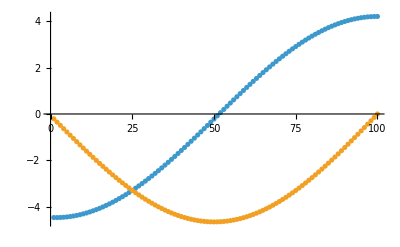
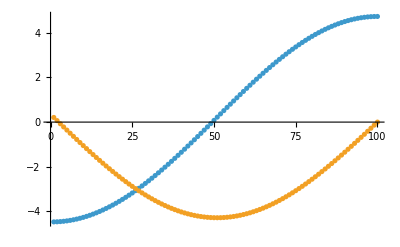
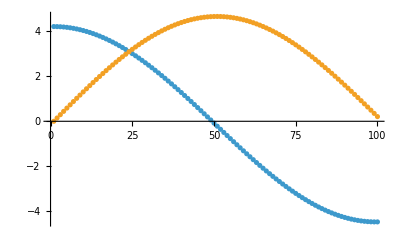
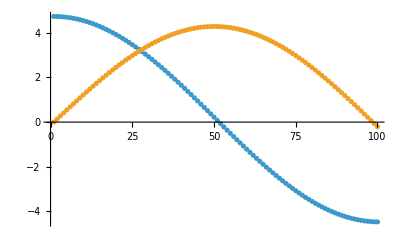

```mathematica
Table[ListPlot[{Re[roots["rootsPaths"][[r,All]]],Im[roots["rootsPaths"][[r,All]]]}], {r,4}]
```

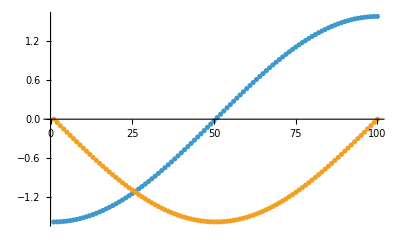
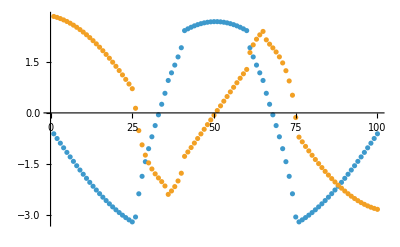
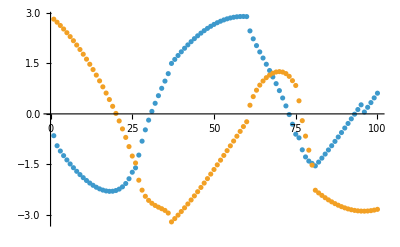
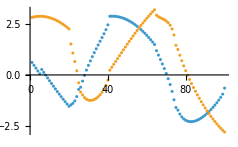
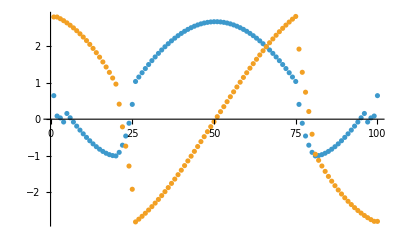
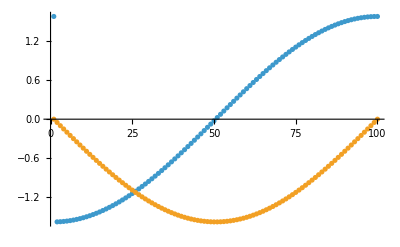

```mathematica
Table[ListPlot[{Re[data[[All,r]]],Im[data[[All,r]]]}], {r,Length[data[[1]]]}]
```

```mathematica
data2=Table[N[{a1[1,20Exp[2Pi I t],2], a2[1,20Exp[2Pi I t],2]},30], {t,roots["tValues"]}];
```

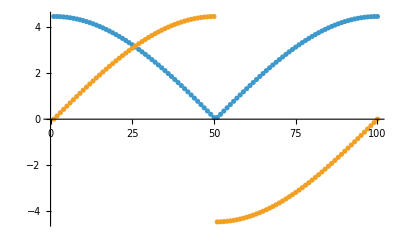
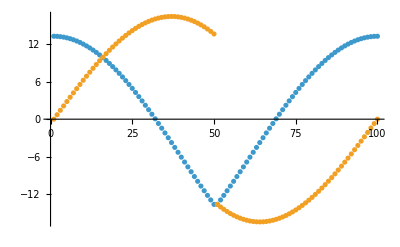

```mathematica
{ListPlot[{Re[data2[[All,1]]], Im[data2[[All,1]]]}], ListPlot[{Re[data2[[All,2]]], Im[data2[[All,2]]]}]}
```

```mathematica
Table[{a,b,c}.Prepend[data2[[i]],1]==data[[i,1]], {i,{1,7,15}}];
Chop[Solve[%,{a,b,c}],10^-5]
```

{{a→0,b→-0.35355739172177691350901833757,c→0}}

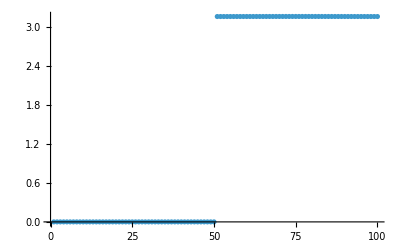

```mathematica
ListPlot[Abs/@Table[{0,-0.353557391721776913,0}.Prepend[data2[[r]],1]-data[[r,1]], {r,Length[data]}]]
```

```mathematica
Table[{a,b,c}.Prepend[data2[[i]],1]==data[[i,5]], {i,{2,7,15}}];
sol=Chop[First@Solve[%,{a,b,c}],10^-5]
```

{a→14.445263853988077410422080441+4.4572353532452867290372178844 ⅈ,b→-7.4025448715151848698070091511-0.83895119808472660364755760334 ⅈ,c→1.4071707061447471644931696791+0.16162973793843061167858769405 ⅈ}

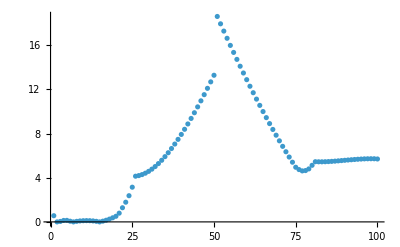

```mathematica
ListPlot[Table[Abs[({a,b,c}.Prepend[data2[[r]],1]/.sol)-data[[r,5]]], {r,Length[data]}]]
```

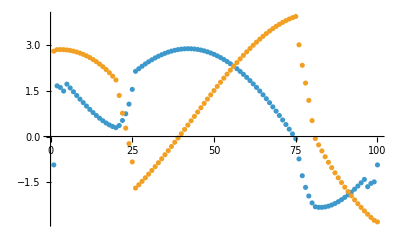

```mathematica
ListPlot[{Re[data[[All,5]]-data[[All,6]]],Im[data[[All,5]]-data[[All,6]]]},PlotRange->All]
```

```mathematica
s1=Assuming[w>0,Simplify[Series[D[a1[m,1/w,0],w],{w,0,3}]]]
```

-1/(2 w^(3/2))-(3 m √w)/32+(15 w^(3/2))/2048-(105 m^2 w^(5/2))/2048+O[w]^(7/2)

```mathematica
s2=Assuming[w>0,Simplify[Series[D[3a2[m,1/w,0],w],{w,0,3}]]]
```

(3 (-2+Log[w]))/(2 w^(3/2))-m^2/(2 √w)+1/32 (-8 m^4+9 m Log[w]) √w+((36-960 m^3-1024 m^6-135 Log[w]) w^(3/2))/6144-((m^2 (-111+224 m^3+256 m^6-315 Log[w])) w^(5/2))/2048+O[w]^(7/2)

```mathematica
tauser=Series[Normal[s2-6s1]/Normal[s1],{w,0,3}]
```

-3 Log[w]+m^2 w+1/8 (-9 m+4 m^4) w^2+((117+192 m^3+512 m^6) w^3)/1536+O[w]^4

```mathematica
Exp[-tauser]
```

w^3-m^2 w^4+(9 m w^5)/8+1/512 (-39-640 m^3) w^6+O[w]^7

```mathematica
Series[1728KleinInvariantJ[Log[q]/(2Pi I)],{q,0,5}]
h0=Simplify[Series[-4096Normal[%]/.{q->Normal[Exp[-tauser]]}, {w,0,3}]]
```

1/q+744+196884 q+21493760 q^2+864299970 q^3+20245856256 q^4+333202640600 q^5+O[q]^6

-4096/w^3-(4096 m^2)/w^2-(512 (m (-9+8 m^3)))/w-8 (380967-512 m^3+512 m^6)-16 (m^2 (363-224 m^3+256 m^6)) w+(702 m-4968 m^4+3072 m^7-4096 m^10) w^2+(-51611960817/64+7158 m^3-4192 m^6+2560 m^9-4096 m^12) w^3+O[w]^4

```mathematica
FullSimplify[1728g2^3/(g2^3-27g3^2)/.g2g3FromCubic[sw1[x,u],x]]
h1=Simplify[Series[%/.{u->1/w},{w,0,3}]]
```

(16384 (3 m-4 u^2)^3)/(27+32 (8 m^3-9 m u-8 m^2 u^2+8 u^3))

-4096/w^3-(4096 m^2)/w^2-(512 (m (-9+8 m^3)))/w+(432+4096 m^3-4096 m^6)-32 (m^2 (27-112 m^3+128 m^6)) w-16 (m^4 (27-192 m^3+256 m^6)) w^2+(-729/16-108 m^3-64 m^6+2560 m^9-4096 m^12) w^3+O[w]^4

```mathematica
Simplify[h0-h1]
```

-3048168-4944 m^2 w+54 m (13-84 m^3) w^2+(-51611957901/64+7266 m^3-4128 m^6) w^3+O[w]^4

```mathematica
QuarticjInvariant[-m-x+(u-x^2)^2,x]
```

(16384 (3 m-4 u^2)^3)/(27+32 (8 m^3-9 m u-8 m^2 u^2+8 u^3))